Problem 1

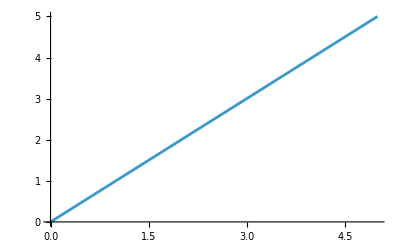

```mathematica
Plot[x,{x,0,5}]
```

Problem 2

```mathematica
D[f[t],t]
D[f[t],{t,2}]
f[t_]:=α Log[a t] Cos[ω t] Sin[ω t]
```

f'[t]

f''[t]

Problem 3

```mathematica
Clear[f]

w[x_]:=f[x] g[x] h[x]
D[w[x],x]
```

g[x] h[x] f'[x]+f[x] h[x] g'[x]+f[x] g[x] h'[x]

Problem 4

{{ϕ→InterpolatingFunction[…]}}

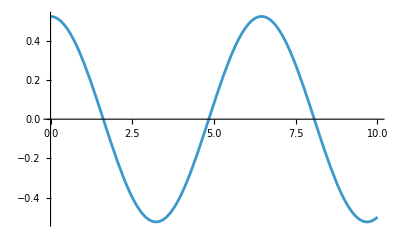

```mathematica
Clear[t,ϕ]
g=9.81;
l=10;
ω=Sqrt[g/l];

sol=NDSolve[{ϕ''[t]==-ω^2 Sin[ϕ[t]],ϕ'[0]==0,ϕ[0]==30 Degree},ϕ,{t,0,10}]
Plot[ϕ[x]/. sol,{x,0,10}]
```

Problem 5

```mathematica
Graphics3D[{Cylinder[{{0,0,0.25},{0,0,6}},0.3],Cylinder[{{0,0,0},{0,0,0.25}}]}]
```

-Graphics3D-